# Data analysis for the Fractal Dimension of the b-LRW on 3d square Lattice

# After optimization

## Import data. MODIFY THE HIGHLIGHTED PARTS EVERY TIME

## b=0 With all the points from the CLUSTER TBD

### Raw data

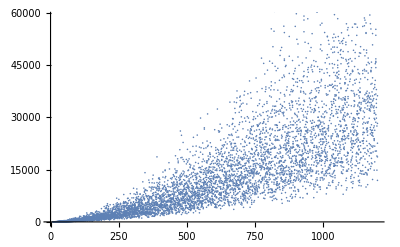

```mathematica
ListPlot[rawData]
```

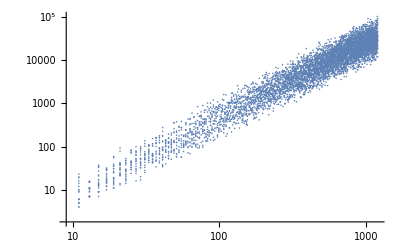

```mathematica
ListLogLogPlot[rawData]
```

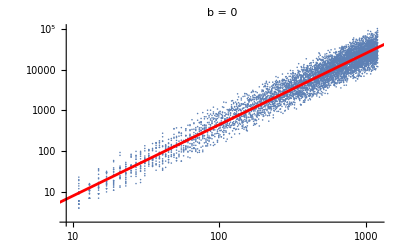

d_f=1.75346±0.00606799
Result from the litterature (exact with SLE): 7/4 = 1.75

```mathematica
lm=LinearModelFit[Log[rawData],x,x];

Show[ListLogLogPlot[rawData],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
,PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

### Drop the first few

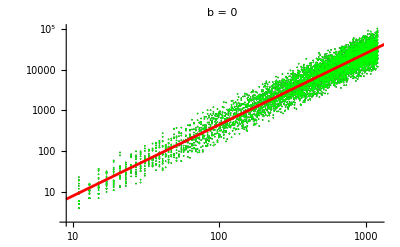

d_f=1.75346±0.00606799
Result from the litterature (exact with SLE): 7/4 = 1.75

```mathematica
threshold=10;

dropped=droppedb0=DeleteCases[rawData,{a_,_}/;a<threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],1000},PlotStyle->Red]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
(*Good enough?*)
```

## b=1 With all the points from the CLUSTER TBD

### Raw data

```mathematica
b=1;
```

```mathematica
rawData=data1=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\b1-clean_merged_data-update.csv"}],"CSV"];
```

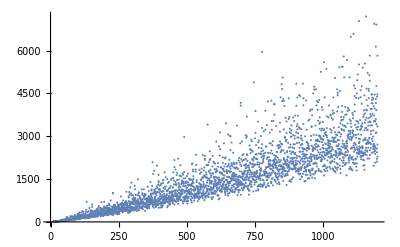

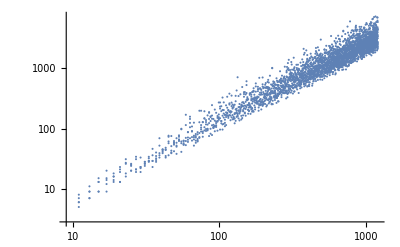

```mathematica
ListPlot[rawData]
ListLogLogPlot[rawData]
```

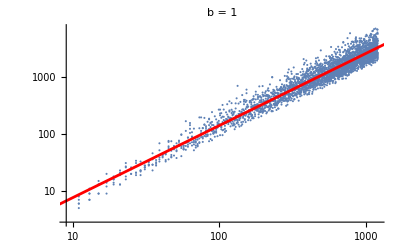

d_f=1.26967±0.00575113
Result from the litterature (exact with SLE): 5/4 = 1.25

```mathematica
lm=LinearModelFit[Log[rawData],x,x];

Show[ListLogLogPlot[rawData],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
,PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

### Drop the first few

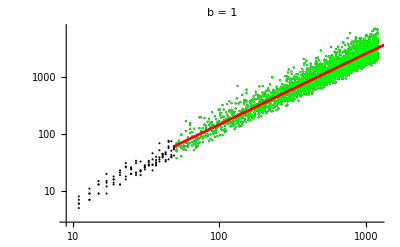

d_f=1.24705±0.00715037
Result from the litterature (exact with SLE): 5/4 = 1.25

```mathematica
threshold=50;

dropped=droppedb1=DeleteCases[rawData,{a_,_}/;a<threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],1000},PlotStyle->Red]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
(*Good enough?*)
```

## b=2 With all the points from the CLUSTER

### Raw data

```mathematica
b=2;

rawData=data2=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\3d-FromCluster\\b2-3d-clean_merged_data.csv"}],"CSV"]; (* MODIFY FILE NAME *)
```

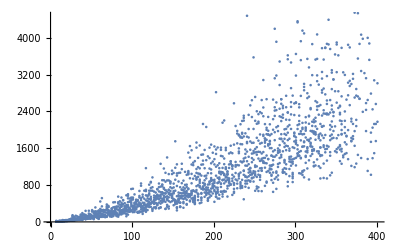

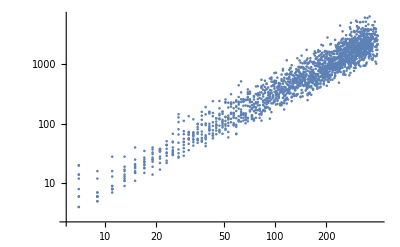

```mathematica
ListPlot[rawData]
ListLogLogPlot[rawData]
```

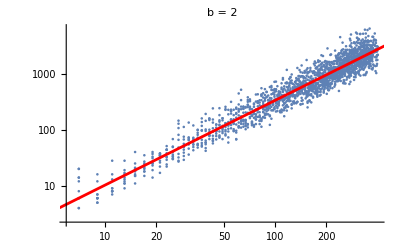

d_f=1.51045±0.0103373
Result from the litterature ??

```mathematica
lm=LinearModelFit[Log[rawData],x,x];

Show[ListLogLogPlot[rawData],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
,PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature ??"]
```

### Drop the first few

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.51648±0.010996
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.50967±0.0127039
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.51125±0.0142729
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.5168±0.0158926
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.52425±0.017598
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.5302±0.0192861
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.5463±0.0210226
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.5471±0.023076
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.54695±0.025137
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.55798±0.0274553
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.56049±0.0300638
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.55476±0.03276
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.56816±0.0359274
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.60279±0.0394417
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.6317±0.0432462
Result from the litterature ??

From all the data: d_f=1.51045±0.0103373
From dropped data: d_f=1.60739±0.0470595
Result from the litterature ??

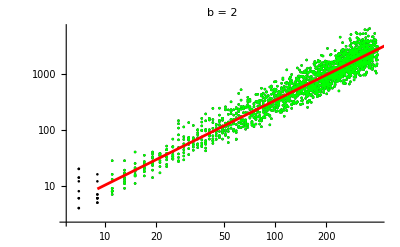
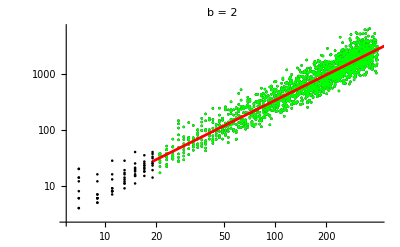
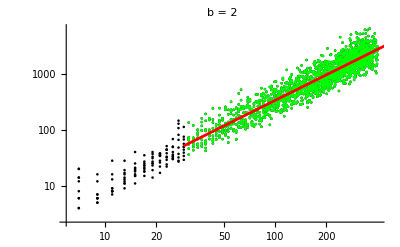
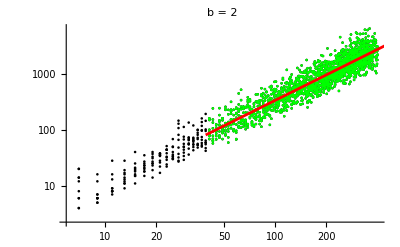
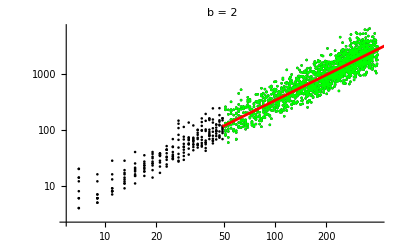
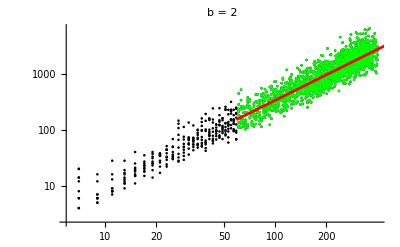
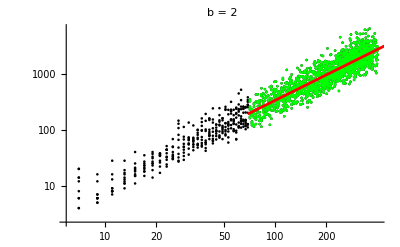
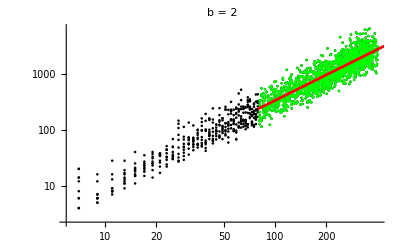
{Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-}

```mathematica
Table[
threshold=10+ii;

dropped=droppedb2=DeleteCases[rawData,{a_,_}/;a<threshold];
lmdropped=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],1000},PlotStyle->Red]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]]

Print[ "From all the data: d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
From dropped data: d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lmdropped["ParameterErrors"][[2]],"
Result from the litterature ?? "]
,{ii,0,150,10}]
```

```mathematica
(*Good enough?*)
```

## b=3 With all the points from the CLUSTER TBD

### Raw data

```mathematica
b=3;
```

```mathematica
data3=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\b3-clean_merged_data.csv"}],"CSV"];
```

```mathematica
rawData=data3;
```

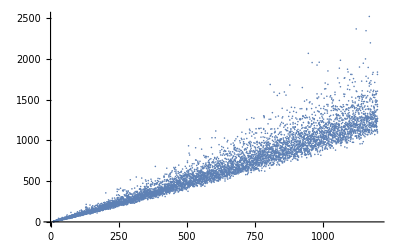

```mathematica
ListPlot[rawData]
```

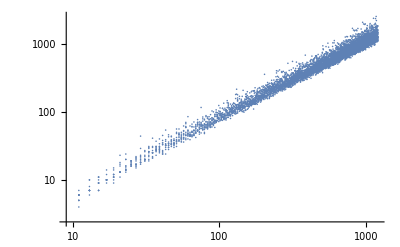

```mathematica
ListLogLogPlot[rawData]
```

```mathematica
Clear[x]
Clear[b]
```

```mathematica
FindFit[Log[rawData],a+df *x,{a,df},x]
```

{a→-0.716314,df→1.1162}

```mathematica
lm=LinearModelFit[Log[rawData],x,x]
```

FittedModel[-0.716314 + 1.1162 x]

```mathematica
lm["ParameterErrors"]
```

{0.00785348,0.00149191}

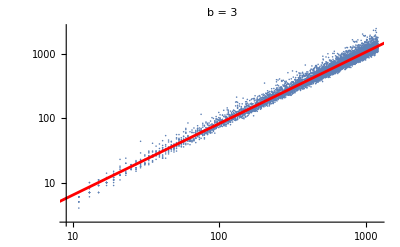

d_f=1.1162±0.00194366
Result from the litterature (exact with SLE): 31/28 = 1.10714

```mathematica
Show[ListLogLogPlot[rawData],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
,PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

### Drop the first few

```mathematica
joinedData=rawData;
```

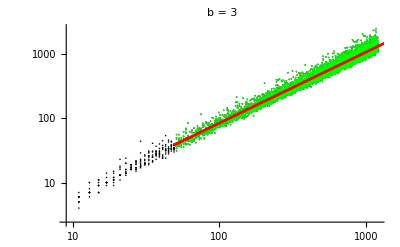

d_f=1.10733±0.00238419
Result from the litterature (exact with SLE): 31/28 = 1.10714

```mathematica
threshold=50;

dropped=droppedb3=DeleteCases[rawData,{a_,_}/;a<threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],1000},PlotStyle->Red]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
(* Very Good !! *)
```

## b=4

## b=4_LRW-3d-square-lattice-data-9_repeat-10000_tol-1e-10-LogSpacing.csv Analysis

### Raw data

```mathematica
b=4;
```

```mathematica
rawData=data4=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\3d\\b=4_LRW-3d-square-lattice-data-9_repeat-10000_tol-1e-10-LogSpacing.csv"}],"CSV"]; (* MODIFY FILE NAME *)
```

70000

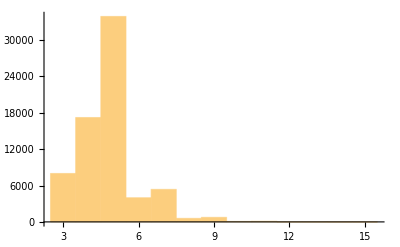

```mathematica
rawData[[All,2]];
Length@%
histoData=%%;
Histogram[#,Length[#],PlotRange->All]&@%
```

## b=4 With all the points from the CLUSTER TBD

### Raw data

```mathematica
b=4;
```

```mathematica
rawData=data4=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\b4-clean_merged_data.csv"}],"CSV"]; (* MODIFY FILE NAME *)
```

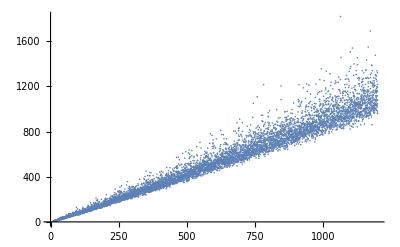

```mathematica
ListPlot[rawData]
```

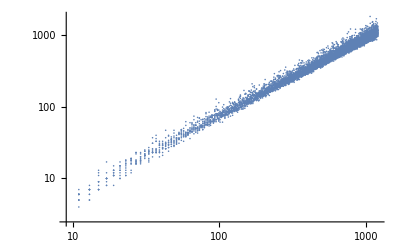

```mathematica
ListLogLogPlot[rawData]
```

```mathematica
FindFit[Log[rawData],a+df *x,{a,df},x]
```

{a→-0.932208,df→1.29378}

```mathematica
lm=LinearModelFit[Log[rawData],x,x]
```

FittedModel[-0.668157 + 1.08285 x]

```mathematica
lm["ParameterErrors"]
```

{0.00785348,0.00149191}

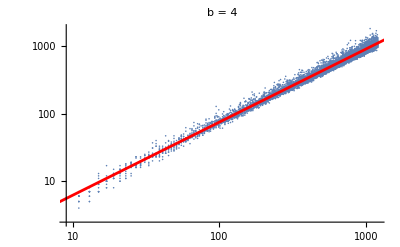

d_f=1.08285±0.00147194
Result from the litterature (exact with SLE): 13/12 = 1.08333

```mathematica
lm=LinearModelFit[Log[rawData],x,x];

Show[ListLogLogPlot[rawData],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
,PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

### Drop the first few

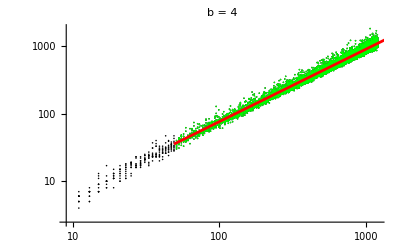

d_f=1.07374±0.00176656
Result from the litterature (exact with SLE): 13/12 = 1.08333

```mathematica
threshold=50;

dropped=droppedb4=DeleteCases[rawData,{a_,_}/;a<threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],1000},PlotStyle->Red]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
(*Good enough?*)
```

## b=5 With all the points from the CLUSTER TBD

### Raw data

```mathematica
b=5;
```

```mathematica
rawData=data5=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\b5-clean_merged_data.csv"}],"CSV"]; (* MODIFY FILE NAME *)
```

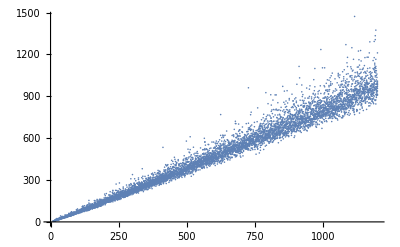

```mathematica
ListPlot[rawData]
```

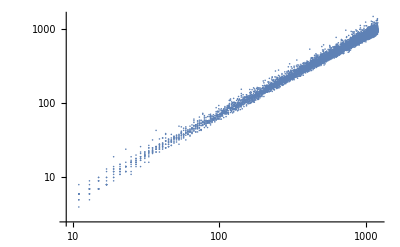

```mathematica
ListLogLogPlot[rawData]
```

```mathematica
FindFit[Log[rawData],a+df *x,{a,df},x]
```

{a→-0.932208,df→1.29378}

```mathematica
lm=LinearModelFit[Log[rawData],x,x]
```

FittedModel[-0.668157 + 1.08285 x]

```mathematica
lm["ParameterErrors"]
```

{0.00785348,0.00149191}

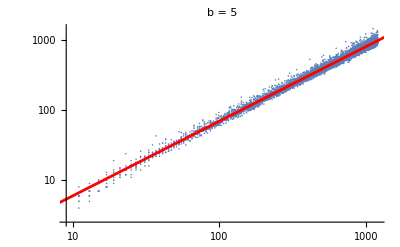

d_f=1.06705±0.00121635
Result from the litterature (exact with SLE): 47/44 = 1.06818

```mathematica
lm=LinearModelFit[Log[rawData],x,x];

Show[ListLogLogPlot[rawData],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
,PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

### Drop the first few

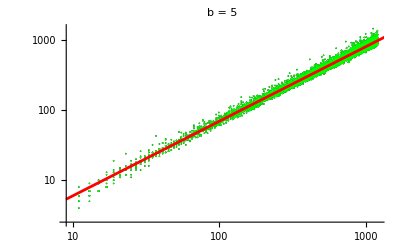

d_f=1.06705±0.00121635
Result from the litterature (exact with SLE): 47/44 = 1.06818

```mathematica
threshold=10;

dropped=droppedb5=DeleteCases[rawData,{a_,_}/;a<threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],1000},PlotStyle->Red]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
(*Good enough?*)
```

## b=10 With all the points from the CLUSTER TBD

### Raw data

```mathematica
b=10;
```

```mathematica
rawData=data10=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\b10-clean_merged_data.csv"}],"CSV"]; (* MODIFY FILE NAME *)
```

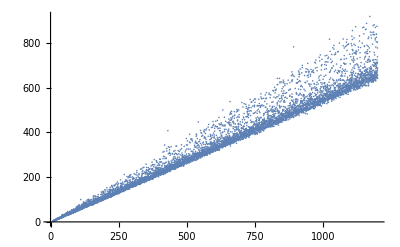

```mathematica
ListPlot[rawData]
```

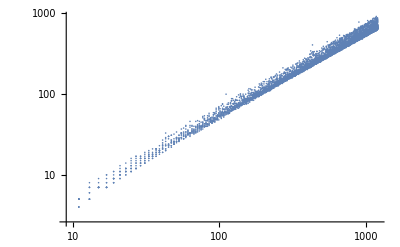

```mathematica
ListLogLogPlot[rawData]
```

```mathematica
FindFit[Log[rawData],a+df *x,{a,df},x]
```

{a→-0.723535,df→1.02507}

```mathematica
lm=LinearModelFit[Log[rawData],x,x]
```

FittedModel[-0.723535 + 1.02507 x]

```mathematica
lm["ParameterErrors"]
```

{0.00734674,0.00118548}

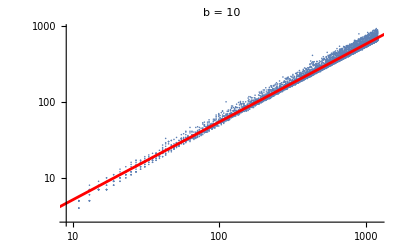

d_f=1.02507±0.00118548
Result from the litterature (exact with SLE): 29/28 = 1.03571

```mathematica
lm=LinearModelFit[Log[rawData],x,x];

Show[ListLogLogPlot[rawData],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
,PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

### Drop the first few

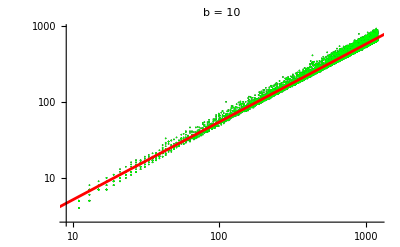

d_f=1.02507±0.00118548
Result from the litterature (exact with SLE): 29/28 = 1.03571

```mathematica
threshold=2;

dropped=droppedb10=DeleteCases[rawData,{a_,_}/;a<threshold];
lm=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],1000},PlotStyle->Red]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
(*Good enough?*)
```

## b=15 With all the points from the CLUSTER TBD

### Raw data

```mathematica
b=15;
```

```mathematica
rawData=data15=ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\b15-clean_merged_data.csv"}],"CSV"]; (* MODIFY FILE NAME *)
```

```mathematica
Sort[data15][[-1]]
```

{1401,713}

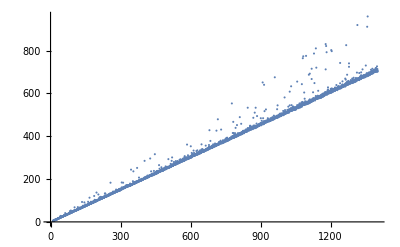

```mathematica
ListPlot[rawData]
```

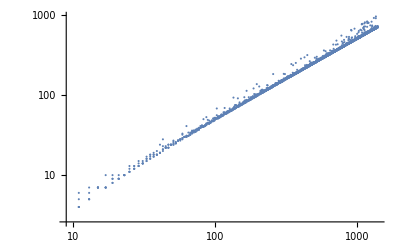

```mathematica
ListLogLogPlot[rawData]
```

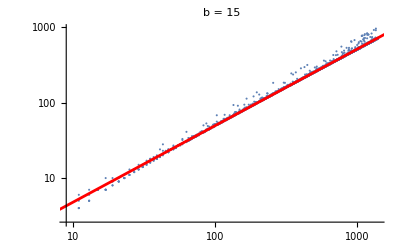

d_f=1.01431±0.00077959
Result from the litterature (exact with SLE): 127/124 = 1.02419

```mathematica
lm=LinearModelFit[Log[rawData],x,x];

Show[ListLogLogPlot[rawData],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
,PlotLabel->Row[{" b = ",b}]]

Print[ "d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

### Drop the first few

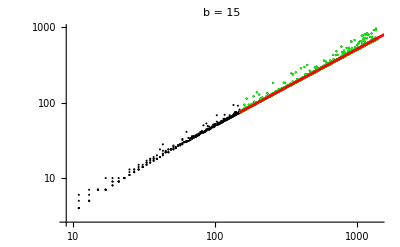

From all the data: d_f=1.01431±0.00077959
From dropped data: d_f=1.00478±0.00115471
Result from the litterature (exact with SLE): 127/124 = 1.02419

```mathematica
threshold=150;

dropped=droppedb15=DeleteCases[rawData,{a_,_}/;a<threshold];
lmdropped=LinearModelFit[Log[dropped],x,x];

Show[{ListLogLogPlot[rawData,PlotStyle->Black],ListLogLogPlot[dropped,PlotStyle->Green],
Plot[lm[x],{x,Log[threshold-1],1000},PlotStyle->Red]}
,(*PlotRange->All,*)PlotLabel->Row[{" b = ",b}]]

Print[ "From all the data: d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
From dropped data: d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lmdropped["ParameterErrors"][[2]],"
Result from the litterature (exact with SLE): ",(dfSLE/.bb->b)," = ",(dfSLE/.bb->b/1.)]
```

```mathematica
(*Good enough?*)
```

## From data, together

```mathematica
droppedList={droppedb0,droppedb1,droppedb2,droppedb3,droppedb4,droppedb5,droppedb10};

lmList=LinearModelFit[Log[#],x,x]&/@droppedList;
```

```mathematica
flatList=Table[Replace[droppedList[[i]],{x_,y_}:>{x,y/(x^lmList[[i]]["BestFitParameters"][[2]])},1],{i,1,Length@droppedList}];
```

$Aborted

```mathematica
lm1=LinearModelFit[Log[droppedb1],x,x];
lm2=LinearModelFit[Log[droppedb2],x,x];
lm3=LinearModelFit[Log[droppedb3],x,x];
lm4=LinearModelFit[Log[droppedb4],x,x];
lm5=LinearModelFit[Log[droppedb5],x,x];
lm10=LinearModelFit[Log[droppedb10],x,x];
```

```mathematica
lm1["ParameterErrors"][[2]]
lm2["ParameterErrors"][[2]]
lm3["ParameterErrors"][[2]]
lm4["ParameterErrors"][[2]]
lm5["ParameterErrors"][[2]]
```

0.0232706

0.0134148

0.0146428

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partw: Part 2 of LinearModelFit[Log[joinedDatab4],x,x][ParameterErrors] does not exist.

LinearModelFit[Log[joinedDatab4],x,x][ParameterErrors]⟦2⟧

0.00640939

```mathematica
lm1["BestFitParameters"][[2]]
```

1.27452

```mathematica
droppedb1;
flat1=Replace[%,{x_,y_}:>{x,y/(x^lm1["BestFitParameters"][[2]])},1];
```

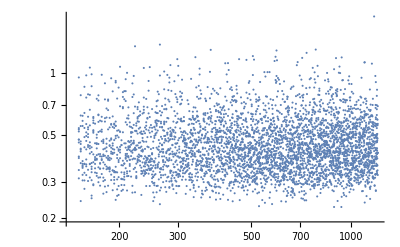

```mathematica
ListLogLogPlot[flat1]
```

```mathematica
ListLogLogPlot[droppedb1-{},PlotStyle->{Black}]
```

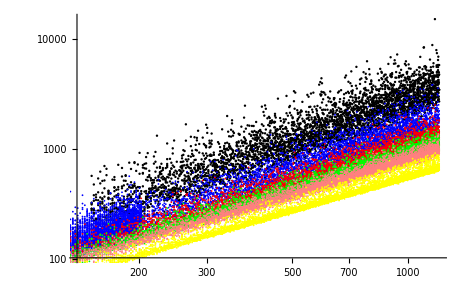

```mathematica
Show[{ListLogLogPlot[droppedb1,PlotStyle->{Black}],
ListLogLogPlot[droppedb2,PlotStyle->{Blue}],
ListLogLogPlot[droppedb3,PlotStyle->{Red}],
ListLogLogPlot[droppedb4,PlotStyle->{Green}],
ListLogLogPlot[droppedb5,PlotStyle->{Pink}],
ListLogLogPlot[droppedb10,PlotStyle->{Yellow}]}]
```

## Compare with Analytic result

## Compared with SLE

```mathematica
droppedList={droppedb0,droppedb1,droppedb2,droppedb3,droppedb4,droppedb5,droppedb10};

lmList=LinearModelFit[Log[#],x,x]&/@droppedList;
```

```mathematica
Table[{i,Around[lmList[[i+1]]["BestFitParameters"][[2]],lmList[[i+1]]["ParameterErrors"][[2]]]},{i,0,6}](* Last one is actually 10 *)
```

{{0,1.7530.006},{1,1.2750.008},{2,1.16590.0019},{3,1.10730.0024},{4,1.07370.0018},{5,1.06700.0012},{6,1.02510.0012}}

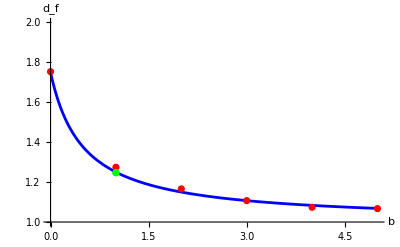

```mathematica
endRange=5;

Simulation2d=ListPlot[{{0,1.7530.006},{1,1.2750.008},{2,1.16590.0019},{3,1.10730.0024},{4,1.07370.0018},{5,1.06700.0012}(*,{10,1.02510.0012}*)},PlotStyle->Red];

Simulation2dupdated=ListPlot[{{1,Around[1.2470465422247456,0.0071503660373209805]}},PlotStyle->Green];

plotSLE=Plot[dfSLE,{bb,0,endRange},PlotStyle->Blue,PlotRange->All];

Show[{plotSLE,Simulation2d,Simulation2dupdated},PlotRange->{1,2},AxesLabel->{"b",Subscript[d, f]},AxesOrigin->{0,1}]
```

### Normalize wrt SLE

```mathematica
{{0,1.7530.006},{1,1.2750.008},{2,1.16590.0019},{3,1.10730.0024},{4,1.07370.0018},{5,1.06700.0012},{10,1.02510.0012}}/.{a_,b_}:>{a,(b-1)/(dfSLE-1./.bb->a)}
```

```mathematica
{1,Around[1.2470465422247456,0.0071503660373209805]}/.{a_,b_}:>{a,(b-1)/(dfSLE-1./.bb->a)}
```

{1,0.9880.029}

```mathematica
dfSLE-1./.bb->10
```

0.0357143

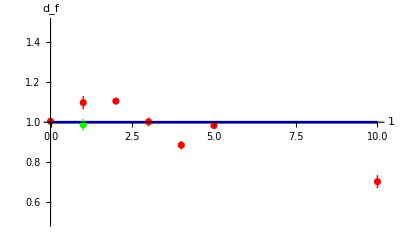

```mathematica
endRange=10;

Simulation2dnorm=ListPlot[{{0,1.0050.008},{1,1.0980.033},{2,1.1060.013},{3,1.0020.022},{4,0.8850.021},{5,0.9830.018},{10,0.7020.033}},PlotStyle->Red];

Simulation2dupdatedNorm=ListPlot[{{1,0.9880.029}},PlotStyle->Green];

plotSLEnorm=Plot[(dfSLE-1)/(dfSLE-1),{bb,0,endRange},PlotStyle->Blue,PlotRange->All];

Show[{plotSLEnorm,Simulation2dnorm,Simulation2dupdatedNorm},PlotRange->{0.5,1.5},AxesLabel->{b,Subscript[d, f]},AxesOrigin->{0,1}]
```